```mathematica
w[t_,f_] :=Sin[2*Pi*f*(t-t0)]
```

```mathematica
w[t,f]
```

Sin[2 f π (t-t0)]

```mathematica
Manipulate[Plot[Sin[2 f π (t-t0)],{t,0,2}],{{f,2},0,8,5},{{t0,0},0,2}]
```

```mathematica
r[t_,f_]:=Piecewise[{{0,t<=t0},{(1.0-Cos[Pi*f*(t-t0)])/2, t0<t<=t0+1/f},{1,t>t0+1/f}}]
```

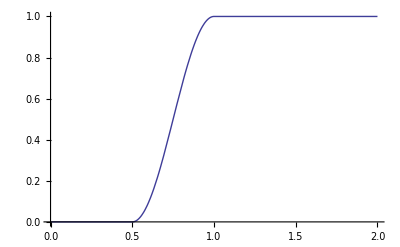

```mathematica
Plot[r[t,f]/.{t0->0.5,f->2},{t,0,2}]
```

```mathematica
wr[t_,f_]:=w[t,f]*r[t,f]
```

```mathematica
Plot[wr[t,f]/.{t0->0.5, f->2},{t,0,2}]
```

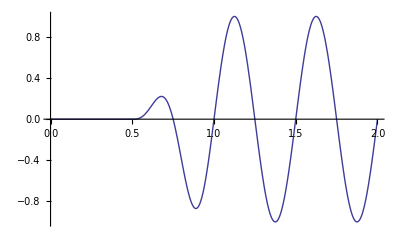

```mathematica
wr[t,f]
```

(Piecewise[{{0, t≤t0}, {1/2 (1.-Cos[f π (t-t0)]), t0<t≤1/f+t0}, {1, t>1/f+t0}, {0, True}}]) Sin[2 f π (t-t0)]

```mathematica
dwr[t_,f_]:=D[wr[t,f], t]
```

```mathematica
dwr[t,f]
```

2 f π Cos[2 f π (t-t0)] (Piecewise[{{0, t≤t0}, {1/2 (1.-Cos[f π (t-t0)]), t0<t≤1/f+t0}, {1, t>1/f+t0}, {0, True}}])+(Piecewise[{{0, t-t0≤0}, {1.5708 f Sin[f π (t-t0)], t-t0>0&&1/f-t+t0≥0}, {0, True}}]) Sin[2 f π (t-t0)]